# Week 2:

```mathematica
SolF=DSolve[x''[t]+2β x'[t]+ω0^2  x[t]==A Cos[ω t],x[t],t]
SolH=DSolve[x''[t]+2β x'[t]+ω0^2  x[t]==0,x[t],t]
Simplify[SolP=SolF-SolH]
```

{{x[t]→ⅇ^(t (-β-√(β^2-ω0^2))) C[1]+ⅇ^(t (-β+√(β^2-ω0^2))) C[2]-(A (-ω^2 Cos[t ω]+ω0^2 Cos[t ω]+2 β ω Sin[t ω]))/((2 β^2+ω^2-ω0^2+2 β √(β^2-ω0^2)) (-2 β^2-ω^2+ω0^2+2 β √(β^2-ω0^2)))}}

{{x[t]→ⅇ^(t (-β-√(β^2-ω0^2))) C[1]+ⅇ^(t (-β+√(β^2-ω0^2))) C[2]}}

{{-(x[t]→ⅇ^(-t (β+√(β^2-ω0^2))) (C[1]+ⅇ^(2 t √(β^2-ω0^2)) C[2]))+(x[t]→ⅇ^(-t (β+√(β^2-ω0^2))) C[1]+ⅇ^(t (-β+√(β^2-ω0^2))) C[2]+(A ((-ω^2+ω0^2) Cos[t ω]+2 β ω Sin[t ω]))/(4 β^2 ω^2+(ω^2-ω0^2)^2))}}

```mathematica
SolP=(A ((-ω^2+ω0^2) Cos[t ω]+2 β ω Sin[t ω]))/(4 β^2 ω^2+(ω^2-ω0^2)^2)
```

```mathematica
res1=(x[t]/.SolF/.{C[1]-> 0,C[2]-> 0})[[1]]
res2=FullSimplify[res1]
```

-(A (-ω^2 Cos[t ω]+ω0^2 Cos[t ω]+2 β ω Sin[t ω]))/((2 β^2+ω^2-ω0^2+2 β √(β^2-ω0^2)) (-2 β^2-ω^2+ω0^2+2 β √(β^2-ω0^2)))

(A ((-ω^2+ω0^2) Cos[t ω]+2 β ω Sin[t ω]))/(4 β^2 ω^2+(ω^2-ω0^2)^2)

```mathematica
Amp= √(((A (-ω^2+ω0^2))/(4 β^2 ω^2+(ω^2-ω0^2)^2))^2+((2 β ω)/(4 β^2 ω^2+(ω^2-ω0^2)^2))^2);
```

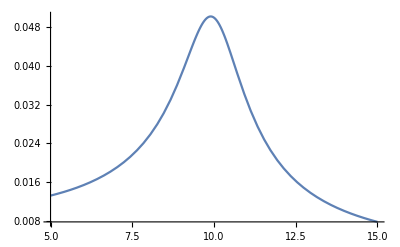

```mathematica
Plot[Amp/.{A->1,ω0-> 10,β-> 1},{ω,5,15}]
```

```mathematica
Phase1=ArcTan[(A (-ω^2+ω0^2))/(2 β ω)]
```

ArcTan[(A (-ω^2+ω0^2))/(2 β ω)]

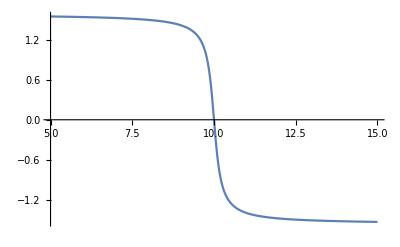

```mathematica
Plot[Phase1/.{A->6,ω0-> 10,β-> 1},{ω,5,15}]
```

השורה מטה מהווה לי כלל הצבה. עלי להגדיר איזה פונקציה אני רוצה שתקיים את כלל זה, וזה נעשה בצורה שכתובה מטה-
Pt=...

```mathematica
s=NDSolve[{x''[t]+2 x'[t]+x[t]== Cos[t],x[0]==0,x'[0]==0},x,{t,0,10}]
```

{{x→InterpolatingFunction[…]}}

```mathematica
{{x->InterpolatingFunction[…]}}
```

Don’t forget to use Flatten - or else you can’t use the ParametricPlot - the pt is a list of lists and the Parametric Plot function doesn’t like that input, it agrees only to regular lists (“Flat” lists).

```mathematica
pt=Flatten[{x[t]/.s,D[x[t]/.s,t]}]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

Phase space solution for all parameters equal to 1.

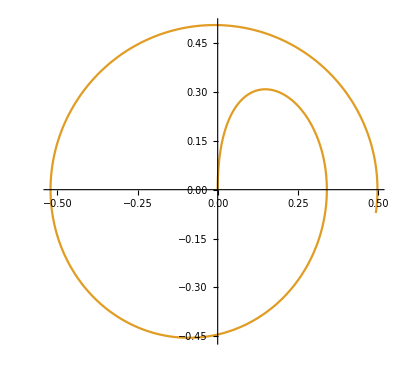

```mathematica
ParametricPlot[pt,{t,0,8}]
```